```mathematica
<<peeters`
peeters`setGitDir["../project/figures/GAelectrodynamics"]
```

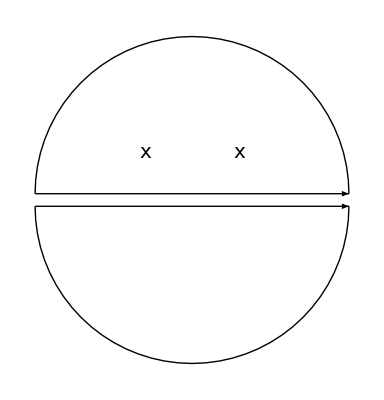

```mathematica
ClearAll[sh, r, fs, greensFunctionContoursFigure]
sh=0.4;
r = 10;
fs = Style[#,FontSize -> 20] &;
greensFunctionContoursFigure = Graphics[{
Thick,
Circle[{0.0,sh},r,{0, Pi}],
Circle[{0.0,-sh},r,{Pi, 2 Pi}],
Arrow[{{-r, sh},{r,sh}}],
Arrow[{{-r, -sh},{r,-sh}}],
Text["x"//fs , {3,3}],
Text["x"//fs , {-3,3}]
}]
```

```mathematica
peeters`exportForLatex["greensFunctionContoursFigure",greensFunctionContoursFigure]
```

{greensFunctionContoursFigure.eps,greensFunctionContoursFigurepn.png}